```mathematica
f[x_]:=2x-1;
g[x_]:=x^2;
h[x_]:=1-x;
f[g[h[x]]]//Expand//TraditionalForm
```

2 x^2-4 x+1

```mathematica
(sin(2 x))/(sin(2 x)+1)
```

sin((2 x)/(x+1))

x/(2 x+1)

sin(2 sin(2 x))

```mathematica
Limit[1/(t Sqrt[t+1]) - 1/t,t->0]
```

-1/2

0

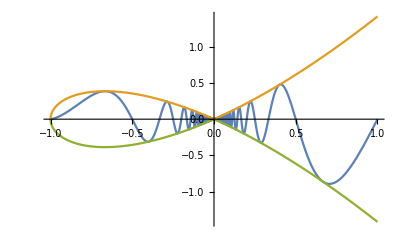

```mathematica
f[x_]:=Sqrt[x^3+x^2]Sin[Pi/x];
Limit[f[x],x->0]
Plot[{f[x],Sqrt[x^3+x^2],-Sqrt[x^3+x^2]},{x,-1,1}]
```

```mathematica
Limit[(2x+12)/Abs[x+6],x->-6,Direction->1]
```

-2

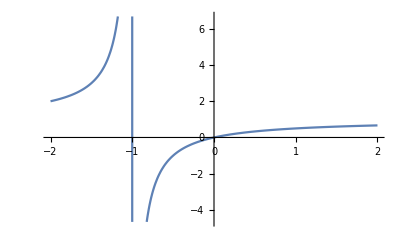

```mathematica
f[x_]:=x/(x+1);
Plot[f[x],{x,-2,2},AxesOrigin->{0,0}]
```